# 1.4 Two-dimensional linear system

### Part a)

```mathematica
M = {{σ+1,3},{-2,σ-1}}
```

{{1+σ,3},{-2,-1+σ}}

```mathematica
MatrixForm[M]
```

(1+σ | 3
-2 | -1+σ)

```mathematica
Eigenvalues[M]
```

{-ⅈ √5+σ,ⅈ √5+σ}

So the eigenvalues are σ - i Sqrt[5] and σ + i Sqrt[5]

### Part b)

```mathematica
eqns={x'[t]==(σ+1)*x[t]+3*y[t],y'[t]==-2*x[t]+(σ-1)*y[t],x[0]==u,y[0]==v};
sol=DSolve[eqns,{x,y},t]//Flatten
```

{x→Function[{t},1/5 ⅇ^(t σ) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])],y→Function[{t},-1/5 ⅇ^(t σ) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])]}

```mathematica
x1 = sol[[1,2,2]]
```

1/5 ⅇ^(t σ) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])

```mathematica
y1 = sol[[2,2,2]]
```

-1/5 ⅇ^(t σ) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])

So that the solutions are x1(t) and y1(t) above.

### Part c)

```mathematica
s = 1/10
```

1/10

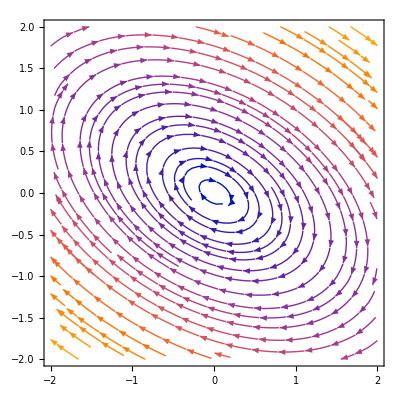

```mathematica
p1 = StreamPlot[{(s+1)*x+3*y, -2*x+(s-1)*y },
 {x,-2 , 2},{y ,-2, 2}]
```

```mathematica
minx = -2;
miny = -2;
maxx = 2;
maxy = 2;
```

```mathematica
sol[x0_ , y0_] :=NDSolve[
{x'[t]== (s+1)*x[t]+3*y [t], 
y'[t] == -2*x[t]+(s-1)*y[t], x[0] == x0 , y[0] == y0} 
, {x,y} , {t,0,27}]
```

```mathematica
dz = 0.2
```

0.2

```mathematica
z = 0.
```

```mathematica
initialC=Tuples[{Range[-0.1,0.1,dz],Range[-0.1,0.1,dz]}]
```

{{-0.1,-0.1},{-0.1,0.1},{0.1,-0.1},{0.1,0.1}}

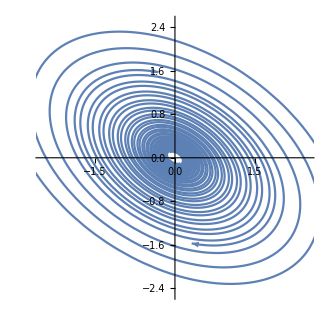

```mathematica
p2 = Show[
Table[
ParametricPlot[
Evaluate[{x[t] , y[t]}/. sol[initialC[[i,1]] , initialC[[i,2]]]]
,{t,0,27} , PlotRange->{{minx-0.5,maxx+0.5} , {miny-0.5,maxy+0.5}}],
{i,1,Length[initialC]}]/. Line[x_] :> {Arrowheads[{0.01,0.08,0.08,0.08,0.07}], Arrow[x]}
]
```

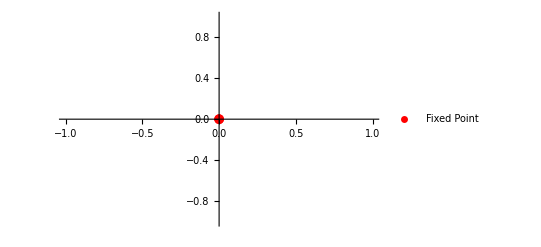

```mathematica
p3 = ListPlot[{{0,0}}, PlotMarkers->{Automatic,10}, PlotStyle -> Red,PlotLegends->{"Fixed Point"} ]
```

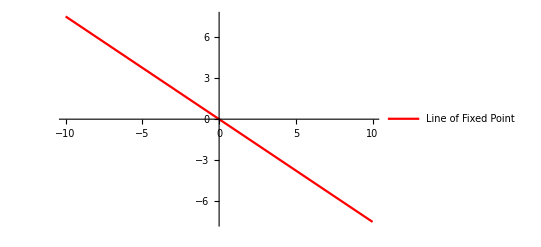

```mathematica
p4 = Plot[-3/4*x, {x,-10,10}, PlotStyle -> Red,PlotLegends->{"Line of Fixed Point"} ]
```

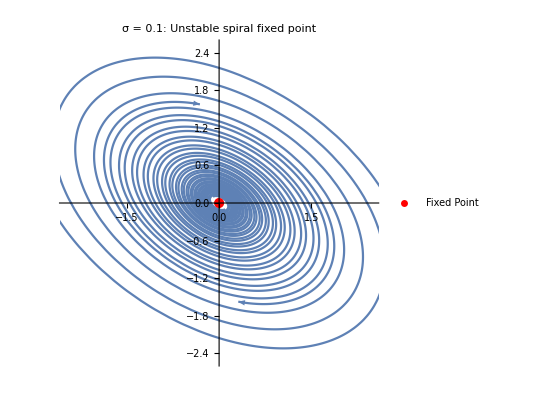

```mathematica
Show[p2,p3, PlotLabel-> "σ = 0.1: Unstable spiral fixed point"]
```

To see that it is unstable, note that the trajectories don’t move towards the red points since there is some white space around it without any trajectories. If the point was stable,  the trajectories would already have been much closer to the fixed point.

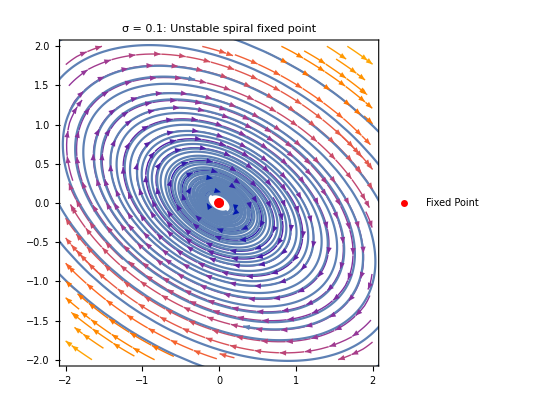

```mathematica
Show[p1,p2,p3, PlotLabel-> "σ = 0.1: Unstable spiral fixed point"]
```

### Part d)

From part b), we see that  when σ = 0, the solutions are purely periodic (no exponential term)  with the period is given by 2 π/Sqrt[5]

### Part e)

For this part, we use "https://en.wikipedia.org/wiki/Ellipse" as a source . The idea is the following : 
   
Note that X = A*T , where X = {x1, y1} and 
T = {cos (sqrt (5)*t), sin (sqrt (5)*t)} for some matrix A (see part b) . Thus T = A^-1 X .  Now note that T[1]^2 + T[2]^2 = cos^2+sin^2=  1, such that 
(A^-1 X)[1]^2 + (A^-1 X)[2]^2 = 1, which gives an equation in purely x1 and y1 . This can be compared with the formula for a general ellipse (which can be rotated and translated) : a*x^2 + b*x*y + c*y^2 + d*x + e*y + f = 0
which is an ellipse if b^2-4*a*c<0

```mathematica
A = {{(3v+u)/Sqrt[5],u},{-(2u+v)/Sqrt[5],v}}
```

{{(u+3 v)/(√5),u},{(-2 u-v)/(√5),v}}

```mathematica
MatrixForm[A]
```

((u+3 v)/(√5) | u
(-2 u-v)/(√5) | v)

```mathematica
B = Inverse[A]//Simplify
```

{{(√5 v)/(2 u^2+2 u v+3 v^2),-(√5 u)/(2 u^2+2 u v+3 v^2)},{(2 u+v)/(2 u^2+2 u v+3 v^2),(u+3 v)/(2 u^2+2 u v+3 v^2)}}

```mathematica
MatrixForm[B]
```

((√5 v)/(2 u^2+2 u v+3 v^2) | -(√5 u)/(2 u^2+2 u v+3 v^2)
(2 u+v)/(2 u^2+2 u v+3 v^2) | (u+3 v)/(2 u^2+2 u v+3 v^2))

```mathematica
(B[[1,1]]*x+B[[1,2]]*y)^2+(B[[2,1]]*x+B[[2,2]]*y)^2 ==1//Simplify
```

(2 x^2+2 x y+3 y^2)/(2 u^2+2 u v+3 v^2)==1

```mathematica
So we see that:
```

```mathematica
a = 2/(2 u^2+2 u v+3 v^2)
```

2/(2 u^2+2 u v+3 v^2)

```mathematica
b = 2/(2 u^2+2 u v+3 v^2)
```

2/(2 u^2+2 u v+3 v^2)

```mathematica
c = 3/(2 u^2+2 u v+3 v^2 )
```

```mathematica
3/(2 u^2+2 u v+3 v^2)
```

```mathematica
f = -1
```

-1

and all other parameters are zero . This is an (rotated) ellipse (with centre the origin ) since

```mathematica
b^2-4*a*c
```

-20/((2 u^2+2 u v+3 v^2)^2)

So b^2 - 4*a*c < 0. The eccentricity of the ellipse is then given by (see https://en.wikipedia.org/wiki/Eccentricity_(mathematics) )

```mathematica
e = Sqrt[2*Sqrt[(a-c)^2+b^2]/(a+c+Sqrt[(a-c)^2+b^2])]//Simplify
```

√2 5^(1/4) √((√(1/((2 u^2+2 u v+3 v^2)^2)))/(√5 √(1/((2 u^2+2 u v+3 v^2)^2))+5/(2 u^2+2 u v+3 v^2)))

```mathematica
e = Simplify[e, Assumptions->{2 u^2+2 u v+3 v^2 ∈ Reals}]
```

5^(1/4) √(2/(5+√5))

Now note that the eccentricity = sqrt (1 - b^2/a^2) where a and b are now the minor and major axis . The length ratio q = a/b then equals 
1/sqrt (1 - e^2)

```mathematica
q = 1/Sqrt[1-e^2]//Simplify
```

√(1/2 (3+√5))

```mathematica
RootReduce[q]
```

1/2 (1+√5)

So the length ratio equals (1 + sqrt (5))/2 = golden ratio!

### Part f)

Following https://en.wikipedia.org/wiki/Matrix_representation_of_conic_sections, the (normalised) vector towards the major axis equals the eigenvector with smallest eigenvalue of the quadratic form matrix L :

```mathematica
L = {{a,b/2},{b/2,c}}
```

{{2/(2 u^2+2 u v+3 v^2),1/(2 u^2+2 u v+3 v^2)},{1/(2 u^2+2 u v+3 v^2),3/(2 u^2+2 u v+3 v^2)}}

```mathematica
MatrixForm[L]
```

(2/(2 u^2+2 u v+3 v^2) | 1/(2 u^2+2 u v+3 v^2)
1/(2 u^2+2 u v+3 v^2) | 3/(2 u^2+2 u v+3 v^2))

```mathematica
eig = Eigensystem[L]
```

{{(5+√5)/(2 (2 u^2+2 u v+3 v^2)),(5-√5)/(2 (2 u^2+2 u v+3 v^2))},{{1/2 (-1+√5),1},{1/2 (-1-√5),1}}}

So the eigenvector with smallest eigenvalue is k ={1/2 (-1-√5),1} and is thus the vector pointing along the major axis. This vector is not normalised yet.

```mathematica
k = eig[[2,2]]
```

{1/2 (-1-√5),1}

```mathematica
k =Normalize[k]
```

{(-1-√5)/(2 √(1+1/4 (1+√5)^2)),1/(√(1+1/4 (1+√5)^2))}

```mathematica
k[[1]]
```

(-1-√5)/(2 √(1+1/4 (1+√5)^2))

```mathematica
RootReduce[(-1-√5)/(2 √(1+1/4 (1+√5)^2))]
```

Root-0.851Root[1-5 #1^2+5 #1^4&,1]-0.8506508083520399

```mathematica
ToRadicals[Root[1-5 #1^2+5 #1^4&,1,0]]
```

-√(1/10 (5+√5))

```mathematica
N[-√(1/10 (5+√5))]
```

-0.850651

```mathematica
k[[2]]
```

1/(√(1+1/4 (1+√5)^2))

```mathematica
RootReduce[1/(√(1+1/4 (1+√5)^2))]
```

Root0.526Root[1-5 #1^2+5 #1^4&,3]0.5257311121191336

```mathematica
ToRadicals[Root[1-5 #1^2+5 #1^4&,3,0]]
```

√(1/10 (5-√5))

```mathematica
N[√(1/10 (5-√5))]
```

0.525731

So the normalised vector along the semi-major axis with first component positive equals {√(1/10 (5+√5)), -√(1/10 (5-√5))} = {0.8506,-0.5257}